# The basic example

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=0;
λ=-2.7;
f[z_]=(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1);
z0=.5+.5I;
iter=1000000;
opac=.9;
Timing[Image[Graphics[{Black,Opacity[opac],PointSize[Tiny],Point[ReIm@NestList[f,z0,iter]]}],ImageResolution->50,ImageSize->Large]]
```

{4.17315,-Graphics-}

### Can we get 1,000,000 iterations plotted in under 4 seconds?

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=0;
λ=-2.7;
f=Compile[{{z,_Complex}},(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1)];
pre=Compile[{{z,_Complex}},Quotient[{width,height}*({Re[z],Im[z]}-{xmin,ymin}),{xwidth,ywidth}]]
width=200;
height=200;
xmin=-.8;
xmax=.8;
xwidth=xmax-xmin;
ymin=-.8;
ymax=.8;
ywidth=ymax-ymin;
z[0]=.1+.1I;
z[1]:=f[z[0]];
iter=100000;
(*data0=ConstantArray[0,{width,height}];(* this could be the problem *)*)
data=SparseArray[{},{width,height}];
```

CompiledFunction[…]

```mathematica
pre[.1+I.1]
```

{56,56}

```mathematica
Timing[Do[
{arrayx,arrayy}=pre[z[1]];
data[[arrayx,arrayy]]++;
z[0]=z[1];,{k,1,iter}];
ArrayPlot[data]]
```

{4.22732,-Graphics-}

```mathematica
t={0,0,0};
t[[1]]++
t
```

0

{1,0,0}

```mathematica
t[[1]]++
t
```

1

{2,0,0}

```mathematica
+
```

```mathematica
data0
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},97,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

Make it a compiled function

```mathematica
Timing[Do[
{arrayx,arrayy}=Quotient[{width,height}*(ReIm@z[1]-{xmin,ymin}),{xwidth,ywidth}];
data1[[arrayx,arrayy]]:=data0[[arrayx,arrayy]]+1;
data0=data1;
z[0]=z[1];,{k,1,iter}];
ArrayPlot[data1]]
```

{10.7985,-Graphics-}

```mathematica
Timing[Do[
{arrayx,arrayy}=Ceiling[{width,height}*(ReIm@z[1]-{xmin,ymin})/{xmax-xmin,ymax-ymin}];
data1[[arrayx,arrayy]]:=data0[[arrayx,arrayy]]+1;
data0=data1;
z[0]=z[1];,{k,1,iter}];
ArrayPlot[data1]]
```

{20.4191,-Graphics-}

# An animated example

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
(*ω=-.01; ω=0*)
λ=-2.7;
f[z_,ω_]:=(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1);
z0=.1+.1I;
iter=1000000;
opac=.2;
ListAnimate[Table[Image[Graphics[{Black,Opacity[opac],PointSize[Tiny],Point[ReIm@NestList[f[#,ω]&,z0,iter]]}],ImageResolution->300,ImageSize->Large],{ω,0,.2,.01}]]
```

# Bins and colors

See: https://mathematica.stackexchange.com/questions/211986/symmetric-icons

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=-.1;
λ=-2.7;
f[z_]:=(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1);
z0=.1+.1I;
res=1000;
iterates=1000000;
Timing[Image[Map[Blend[{Black,Purple,Blue,Green,Yellow,Orange,Red,White},1-#^5]&,Rescale@Transpose@N@BinCounts[ReIm/@NestList[f,z0,iterates],{-1,1,1/res},{-1,1,1/res}],{2}],ImageSize->Large]]
(*
Timing[Image[Map[Blend[{Blue,Yellow},#^4]&,1-Rescale[Normal[matrix]^(1/4)],{2}],ImageSize->Large]]
epsilon=1*^-10;
indices=1+Floor[(1-epsilon) res Rescale[dat]];
Timing[Image[Map[Blend[{Red,Orange,Yellow,Green,Blue, Purple, White,Black},#^4]&,1-Rescale[Normal[matrix]^(1/4)],{2}],ImageSize->Large]]
*)
```

```mathematica
Blend[{Black,Purple,Blue,Green,Yellow,Orange,Red,White},1-#^(1/8)]
```

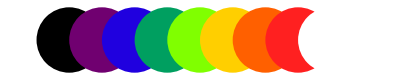

```mathematica
Graphics[Table[{Blend[{Black,Purple,Blue,Green,Yellow,Orange,Red,White},x],Disk[{8x,0}]},{x,0,1,1/8}]]
```

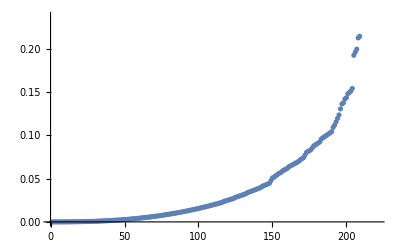

```mathematica
ListPlot@((Sort@DeleteDuplicates@Flatten@Rescale@Transpose@BinCounts[ReIm/@NestList[f,z0,iterates],{-1,1,1/res},{-1,1,1/res}])^(5/2))
```

```mathematica
Timing[dat=ReIm@NestList[f,z0,100000];
res=10;
epsilon=1*^-10;
indices=1+Floor[(1-epsilon) res Rescale[dat]];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->Total}];
matrix=SparseArray[indices->1.,{res,res}];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->First}];
Image[1-Rescale[matrix^(1/4)],ImageSize->Large]]
```

```mathematica
Timing[Image[Map[Blend[{Red,Orange,Yellow,Green,Blue, Purple, White,Black},#^4]&,1-Rescale[Normal[matrix]^(1/4)],{2}],ImageSize->Large]]
```

# Chaos

The behavior of f does seem chaotic.

```mathematica
f[f[f[z0]]]
f[f[f[z0+.01-.01I]]]
```

# Some plots of the function

```mathematica
Plot3D[Im[f[x+I y]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

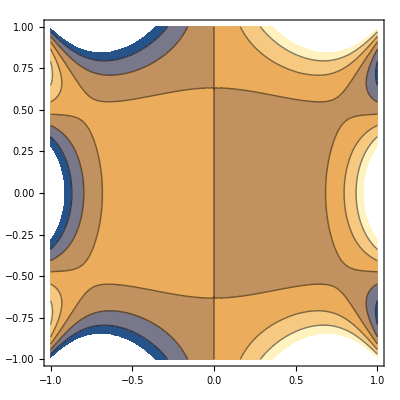

```mathematica
ContourPlot[Re[f[x+I y]],{x,-1,1},{y,-1,1}]
```

# Fractals

```mathematica
GraphicsGrid[Map[MandelbrotSetPlot[#1,ColorFunction->"SunsetColors",Frame->False]&,{{{0.2102 +0.464 I,0.4443 +0.7062 I},Apply[Complex,{{0.2274,0.5529},{0.2455,0.5717}},{1}]},{{},{-0.743+0.175 I,-0.723+0.195 I}}},{2}],ImageSize->600,Frame->All,FrameStyle->Gray]
```

-Graphics-